0<l without a cap

```mathematica
PT1[l_,p_]:=   p^l*(1/2^(l-1))*(1-p)
```

1 < l with cap

```mathematica
PT2[l_,p_]:=p^l/2^(l-1)
```

l=0

```mathematica
PT3[p_]:=1-p
h[τ_]:=1/(1+1/τ)
```

```mathematica
RE1=0.5;
RE2=2;
RE3=20;
T1=Flatten[{PT3[h[RE1]],Evaluate@Table[PT1[l,h[RE1]],{l,1,10}],Evaluate@Table[PT2[l,h[RE1]],{l,2,10}]}];
T2=Flatten[{PT3[h[RE2]],Evaluate@Table[PT1[l,h[RE2]],{l,1,10}],Evaluate@Table[PT2[l,h[RE2]],{l,2,10}]}];
T3=Flatten[{PT3[h[RE3]],Evaluate@Table[PT1[l,h[RE3]],{l,1,10}],Evaluate@Table[PT2[l,h[RE3]],{l,2,10}]}];
T4=Flatten[{PT3[h[100]],Evaluate@Table[PT1[l,h[100]],{l,1,10}],Evaluate@Table[PT2[l,h[100]],{l,2,10}]}];
```

```mathematica
N[Sum[T1[[i]],{i,0,20}]]
N[Sum[T2[[i]],{i,0,20}]]
N[Sum[T3[[i]],{i,0,20}]]
```

1.+List

0.999977+List

0.998858+List

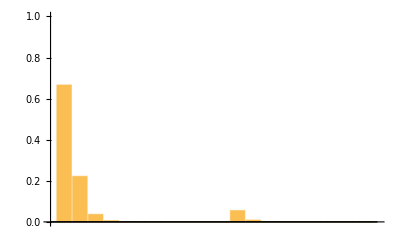

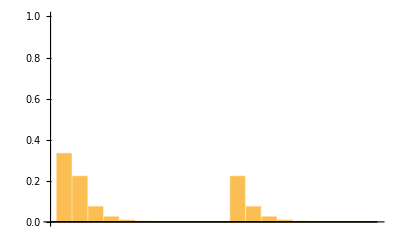

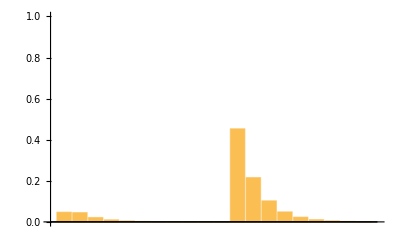

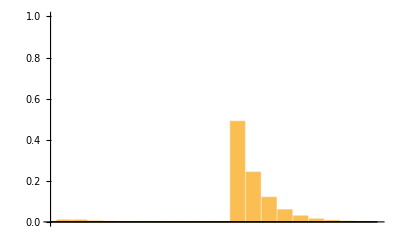

```mathematica
BarChart[T1, PlotRange->{0,1}]
BarChart[T2,PlotRange->{0,1}]
BarChart[T3,PlotRange->{0,1}]
BarChart[T4,PlotRange->{0,1}]
```